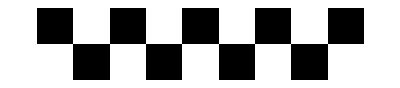

```mathematica
ArrayPlot[{{1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0}}]
```

```mathematica
NumToRegla[num_]:=Module[{lista,numlist,i,base},
lista = {};
numlist = Reverse[IntegerDigits[num,2,8]];
For[i=1,i≤Length[numlist],i++,
base = Reverse[IntegerDigits[i-1,2,3]];
AppendTo[lista,AppendTo[base,numlist[[i]]]];
];
Return[lista];
];
```

```mathematica
NumToRegla[54]
```

{{0,0,0,0},{1,0,0,1},{0,1,0,1},{1,1,0,0},{0,0,1,1},{1,0,1,1},{0,1,1,0},{1,1,1,0}}

```mathematica
NextConfig[estado_,regla_]:=Module[{lenestado,i,triplete,sol,result},
lenestado = Length[estado];
sol = {};
For[i=1,i≤lenestado,i++,
If[i==1,
triplete = {estado[[lenestado]],estado[[i]],estado[[i+1]],_};
,
If[i==lenestado,
triplete = {estado[[i-1]],estado[[i]],estado[[1]],_};
,
triplete = {estado[[i-1]],estado[[i]],estado[[i+1]],_};
];
];
result = Cases[regla,triplete];
AppendTo[sol,result[[1]][[4]]];
];
Return[sol];
];
```

```mathematica
NextConfig[{1,0,1,0,0,0,1,0},{{0,0,0,0},{1,0,0,1},{0,1,0,1},{1,1,0,0},{0,0,1,1},{1,0,1,1},{0,1,1,0},{1,1,1,0}}]
```

{1,1,1,1,0,1,1,1}

```mathematica
Simulacion[inicial_,regla_,t_]:=Module[{reglalist,i,print,estado},
reglalist= NumToRegla[regla];
print = {};
estado=inicial;
AppendTo[print,inicial];
For[i=1,i≤t,i++,
estado = NextConfig[estado,reglalist];
AppendTo[print,estado];
];
Return[ArrayPlot[print]];
];
```

```mathematica
SimulacionAnimate[{1,0,0,1,1,1,0,1,0,0},167,35]
```

```mathematica
SimulacionAnimate[inicial_,regla_,t_]:=Module[{reglalist,i,print,estado,leninicial,sample, j,frame},
reglalist= NumToRegla[regla];
print = {};
estado=inicial;
leninicial = Length[inicial];
sample = {};
frame = {};
For[j=1,j≤leninicial,j++,
AppendTo[sample,1];
];
For[j=1,j≤leninicial,j++,
AppendTo[frame,sample];
];
AppendTo[print,frame];
For[i=1,i≤t,i++,
Rest[frame];
AppendTo[frame,estado];
estado = NextConfig[estado,reglalist];
AppendTo[print, frame];
];
Return[ListAnimate[print]];
];
```